```mathematica
SetDirectory[NotebookDirectory[]];
rasterizeBackground[g_,res_: 100]:=Show[Rasterize[Show[g,PlotRangePadding->0,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res]/.Raster[data_,rect_,rest__]:>Raster[data,Transpose@OptionValue[AbsoluteOptions[g,PlotRange],PlotRange],rest],Sequence@@Options[g],Sequence@@Options[g,PlotRange]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

#### Numerical electrode simulations

{2,10000,1000.}

{0.,0.568298}

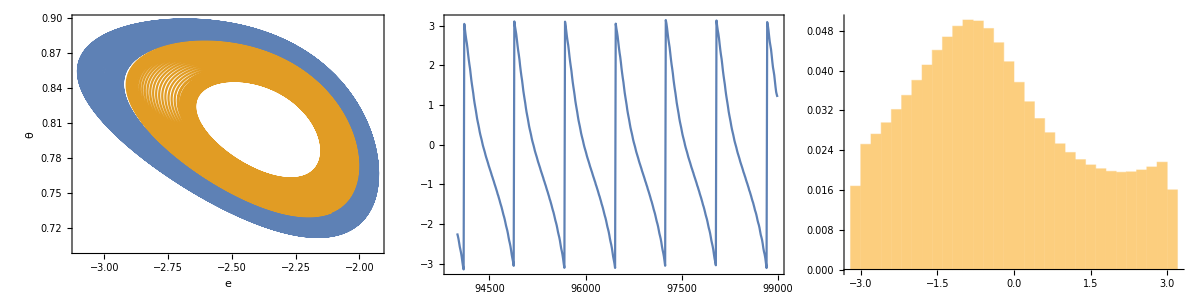
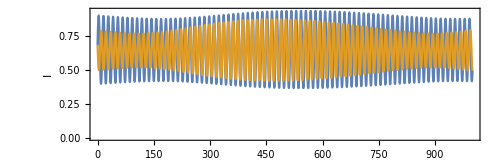

```mathematica
(* Input data and look at limit cycle *)
SetDirectory[NotebookDirectory[]];
file="data/test";
strlst=ReadList[file<>".out",String];
{n,Nt,t1}=ToExpression[StringSplit[strlst[[3]]]][[1;;3]]
ToExpression[StringSplit[strlst[[3]]]][[-2;;-1]]
AbsoluteTiming[dat=Partition[Partition[BinaryReadList[file<>".dat","Real64"], 2],n]];
data=Transpose[dat[[1;;Length[dat]]],{2,1,3}];
pin=BinaryReadList[file<>"phase.dat","Real64"];
p1=ListPlot[data[[All,-5000;;-1]],Joined->True,Axes->False,Frame->True,FrameLabel->{"e",θ},LabelStyle->Directive[16],Joined->True,PlotRange->All,RotateLabel->False];
p2=ListPlot[Transpose[{Range[Length[pin]/2]*t1/Nt,Mod[(-First@Differences[Partition[pin,Length[pin]/2]])+Pi,2*Pi]-Pi}][[-50000;;-1;;100]],Axes->False,Frame->True,Joined->True,PlotRange->{-Pi,Pi}];
p3=Histogram[Mod[-First@Differences[Partition[pin,Length[pin]/2]]+Pi,2*Pi]-Pi,25,"Probability"];
e1=data[[1,All,1]];
theta1=data[[1,All,2]];
e2=data[[2,All,1]];
theta2=data[[2,All,2]];
Ch=1600;
a=0.3;
times=Range[Nt]/Nt*t1;
sig1=(Ch*Exp[0.5*e1]/(1+Ch*Exp[e1])+a*Exp[e1])*(1-theta1);
sig2=(Ch*Exp[0.5*e2]/(1+Ch*Exp[e2])+a*Exp[e2])*(1-theta2);
p4=ListPlot[{Transpose[{times,sig1}][[1;;-1]],Transpose[{times,sig2}][[1;;-1]]},Joined->True,PlotRange->{All,All},AspectRatio->1/3,Frame->True,Axes->False,ImageSize->500,FrameLabel->{t,"I"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]];
Grid[{{Grid[{{p1,p2,p3}}]},{p4}}]
```

{11.5364,Null}

{11.7105,Null}

{11.6826,Null}

{11.7422,Null}

{11.8918,Null}

{11.9461,Null}

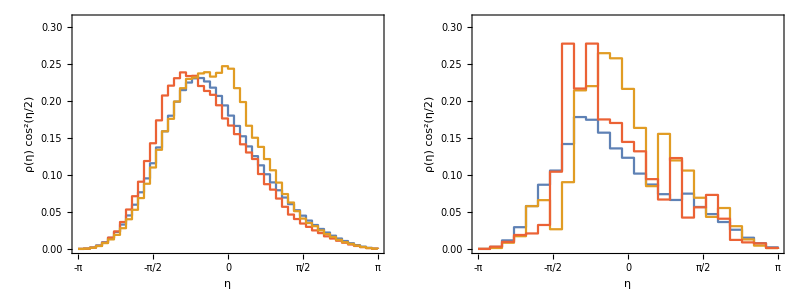

densities.pdf

```mathematica
sigs1=Partition[Internal`StringToDouble/@DeleteCases[StringSplit[Import["data/experiments/exp1.txt"],{"   ","\n"}],""],7];
sigs2=Partition[Internal`StringToDouble/@DeleteCases[StringSplit[Import["data/experiments/exp2.txt"],{"   ","\n"}],""],7];
times1=sigs1[[All,1]];
times2=sigs2[[All,1]];
AbsoluteTiming[p1=getphase[sigs1[[All,2]]];]
AbsoluteTiming[p2=getphase[sigs1[[All,3]]];]
AbsoluteTiming[p3=getphase[sigs1[[All,4]]];]
AbsoluteTiming[p4=getphase[sigs1[[All,5]]];]
AbsoluteTiming[p5=getphase[sigs1[[All,6]]];]
AbsoluteTiming[p6=getphase[sigs1[[All,7]]];]
ediffs1=Mod[p1-p2+Pi,2*Pi]-Pi;
ediffs2=Mod[p3-p4+Pi,2*Pi]-Pi;
ediffs3=Mod[p5-p6+Pi,2*Pi]-Pi;
nbins=25;
plot1=ListPlot[{Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],Table[Cos[i/2]^2/(2*Pi/nbins),{i,-Pi,Pi,2*Pi/nbins}]*N[BinCounts[ediffs1,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[ediffs1])]}],Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],Table[Cos[i/2]^2/(2*Pi/nbins),{i,-Pi,Pi,2*Pi/nbins}]*N[BinCounts[ediffs2,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[ediffs2])]}],Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],Table[Cos[i/2]^2/(2*Pi/nbins),{i,-Pi,Pi,2*Pi/nbins}]*N[BinCounts[ediffs3,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[ediffs3])]}]},InterpolationOrder->0,Joined->True,Axes->False,Frame->True,FrameLabel->{η,Cos[DisplayForm[RowBox[{η,"/",2}]]]^2*ρ[η]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[4]]]},ImageSize->350,PlotRange->{0,0.31},FrameTicks->{{{#,PaddedForm[#,{2,2}]}&/@#,{#,""}&/@#}&@Table[i,{i,0,0.3,0.05}],{{#,#}&/@#,{#,""}&/@#}&@Table[i,{i,-Pi,Pi,Pi/2}]}];
nbins=50;
plot2=ListPlot[{Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],Table[Cos[i/2]^2/(2*Pi/nbins),{i,-Pi,Pi,2*Pi/nbins}]*N[BinCounts[diffs1,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs1])]}],Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],Table[Cos[i/2]^2/(2*Pi/nbins),{i,-Pi,Pi,2*Pi/nbins}]*N[BinCounts[diffs2,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs2])]}],Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],Table[Cos[i/2]^2/(2*Pi/nbins),{i,-Pi,Pi,2*Pi/nbins}]*N[BinCounts[diffs3,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs3])]}]},InterpolationOrder->0,Joined->True,Axes->False,Frame->True,FrameLabel->{η,Cos[DisplayForm[RowBox[{η,"/",2}]]]^2*ρ[η]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[2]]]},ImageSize->350,PlotRange->{0,0.31},FrameTicks->{{{#,PaddedForm[#,{2,2}]}&/@#,{#,""}&/@#}&@Table[i,{i,0,0.3,0.05}],{{#,#}&/@#,{#,""}&/@#}&@Table[i,{i,-Pi,Pi,Pi/2}]}];
plot=Grid[{{plot2,plot1}}]
Export["densities.pdf",plot]
```

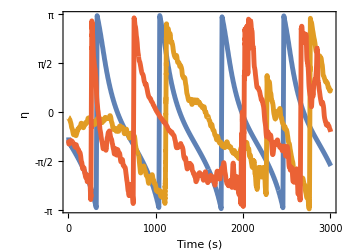
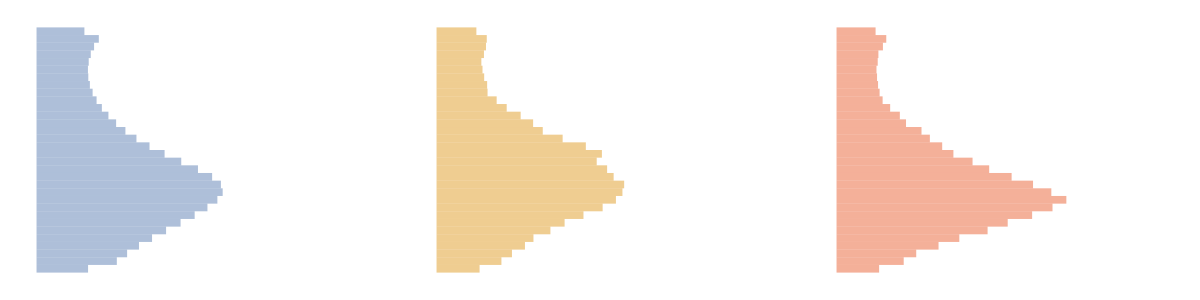
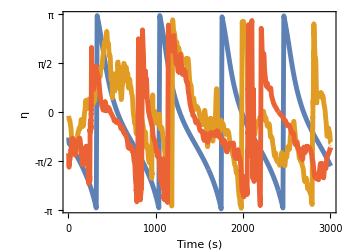
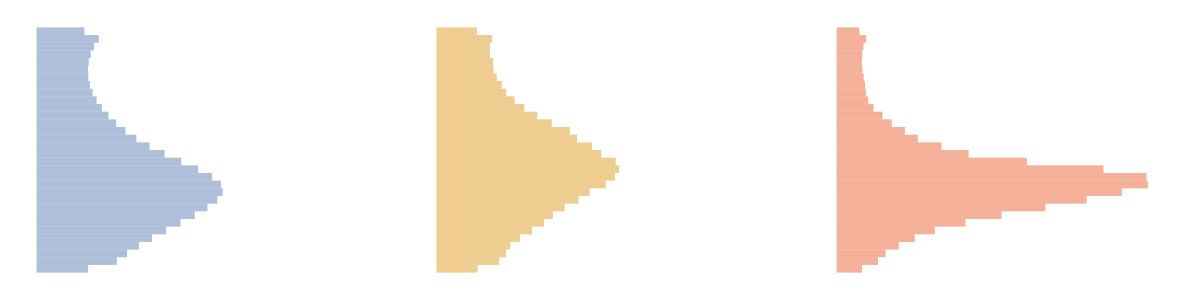
-Graphics- | -Graphics-
-Graphics- | -Graphics-

simulationhistograms.pdf

```mathematica
p=Grid[{{ListPlot[{MovingAverage[Transpose[{Range[Length[diffs1]]*0.1,diffs1}],100],MovingAverage[Transpose[{Range[Length[diffs3]]*0.1,diffs3}],100],MovingAverage[Transpose[{Range[Length[diffs2]]*0.1,diffs2}],100]}[[All,1;;30000]],Joined->True,Frame->True,FrameLabel->{"Time (s)",η},FrameStyle->Directive[AbsoluteThickness[1],Black],LabelStyle->Directive[16,Black], PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[4]]]},ImageSize->{350,275},AspectRatio->(275-55-10)/(350-55-5),ImagePadding->{{55,15},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,-Pi,Pi,Pi/2}],Table[{i,""},{i,-Pi,Pi,Pi/2}]},{Table[i,{i,0,3000,1000}],Table[{i,""},{i,0,3000,1000}]}}],Grid[{{Histogram[diffs1,25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[1]]]},BarOrigin->Left,Axes->False,ImageSize->{100,275},AspectRatio->3,ImagePadding->{{5,10},{55,5}}],Histogram[diffs3,25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[2]]]},BarOrigin->Left,Axes->False,ImageSize->{100,275},AspectRatio->3,ImagePadding->{{5,10},{55,5}}],
Histogram[diffs2,25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[4]]]},BarOrigin->Left,Axes->False,ImageSize->{100,275},AspectRatio->3,ImagePadding->{{5,10},{55,5}}]}}]},{ListPlot[{MovingAverage[Transpose[{Range[Length[diffs1]]*0.1,diffs1}],100],MovingAverage[Transpose[{Range[Length[diffs5]]*0.1,diffs5}],100],MovingAverage[Transpose[{Range[Length[diffs4]]*0.1,diffs4}],100]}[[All,1;;30000]],Joined->True,Frame->True,FrameLabel->{"Time (s)",η},FrameStyle->Directive[AbsoluteThickness[1],Black],LabelStyle->Directive[16,Black], PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[4]]]},ImageSize->{350,275},AspectRatio->(275-55-10)/(350-55-5),ImagePadding->{{55,15},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,-Pi,Pi,Pi/2}],Table[{i,""},{i,-Pi,Pi,Pi/2}]},{Table[i,{i,0,3000,1000}],Table[{i,""},{i,0,3000,1000}]}}],Grid[{{Histogram[diffs1,25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[1]]]},BarOrigin->Left,Axes->False,ImageSize->{100,275},AspectRatio->3,ImagePadding->{{5,10},{55,5}}],Histogram[diffs5,25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[2]]]},BarOrigin->Left,Axes->False,ImageSize->{100,275},AspectRatio->3,ImagePadding->{{5,10},{55,5}}],
Histogram[diffs4,25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[4]]]},BarOrigin->Left,Axes->False,ImageSize->{100,275},AspectRatio->3,ImagePadding->{{5,10},{55,5}}]}}]}}]
Export["simulationhistograms.pdf",p]
```

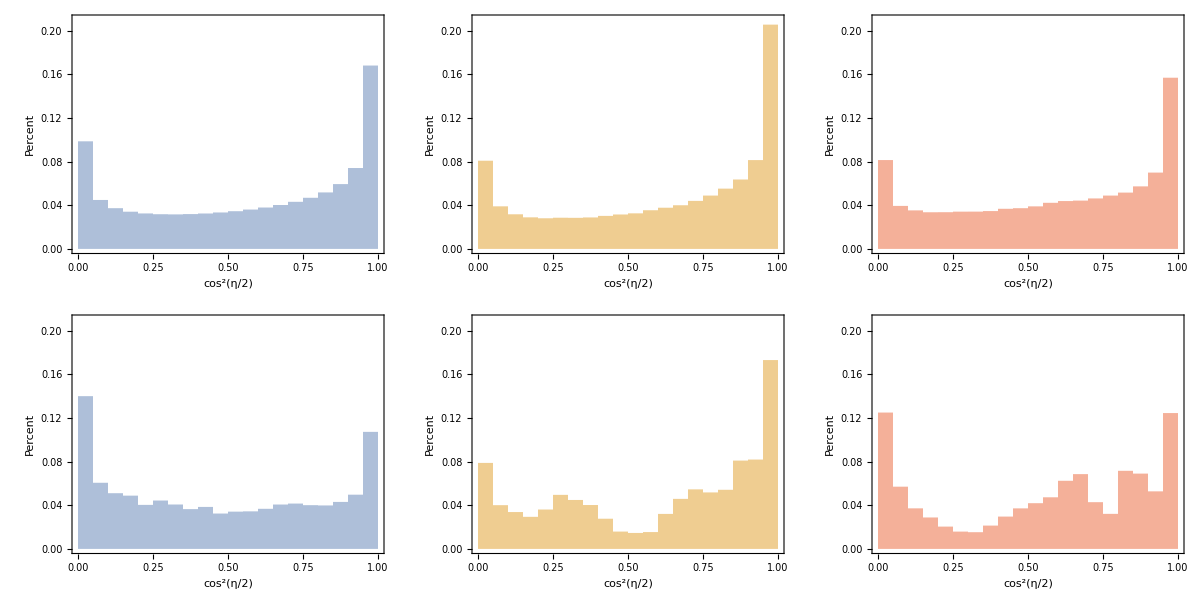

histograms.pdf

```mathematica
p=Grid[{{Histogram[{Cos[(diffs1)/2]^2},25,"Probability",PlotRange->{{0,1},{0,0.21}},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[1]]]},BarOrigin->Bottom,Axes->False,Frame->True,ImageSize->{250,Automatic},ImagePadding->{{65,15},{65,15}},AspectRatio->1,FrameLabel->{Cos[DisplayForm[RowBox[{η,"/",2}]]]^2,"Percent"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]],Histogram[{Cos[(diffs3)/2]^2},25,"Probability",PlotRange->{{0,1},{0,0.21}},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[2]]]},BarOrigin->Bottom,Axes->False,Frame->True,ImageSize->{250,Automatic},ImagePadding->{{65,15},{65,15}},AspectRatio->1,FrameLabel->{Cos[DisplayForm[RowBox[{η,"/",2}]]]^2,"Percent"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]],Histogram[{Cos[(diffs2)/2]^2},25,"Probability",PlotRange->{{0,1},{0,0.21}},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[4]]]},BarOrigin->Bottom,Axes->False,Frame->True,ImageSize->{250,Automatic},ImagePadding->{{65,15},{65,15}},AspectRatio->1,FrameLabel->{Cos[DisplayForm[RowBox[{η,"/",2}]]]^2,"Percent"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]},{Histogram[{Cos[(Mod[p1-p2+Pi,2*Pi]-Pi)/2]^2},25,"Probability",PlotRange->{{0,1},{0,0.21}},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[1]]]},BarOrigin->Bottom,Axes->False,Frame->True,ImageSize->{250,Automatic},ImagePadding->{{65,15},{65,15}},AspectRatio->1,FrameLabel->{Cos[DisplayForm[RowBox[{η,"/",2}]]]^2,"Percent"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]],Histogram[{Cos[(Mod[p3-p4+Pi,2*Pi]-Pi)/2]^2},25,"Probability",PlotRange->{{0,1},{0,0.21}},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[2]]]},BarOrigin->Bottom,Axes->False,Frame->True,ImageSize->{250,Automatic},ImagePadding->{{65,15},{65,15}},AspectRatio->1,FrameLabel->{Cos[DisplayForm[RowBox[{η,"/",2}]]]^2,"Percent"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]],Histogram[{Cos[(Mod[p5-p6+Pi,2*Pi]-Pi)/2]^2},25,"Probability",PlotRange->{{0,1},{0,0.21}},ChartStyle->{Directive[EdgeForm[],Opacity[0.5],ColorData[97,"ColorList"][[4]]]},BarOrigin->Bottom,Axes->False,Frame->True,ImageSize->{250,Automatic},ImagePadding->{{65,15},{65,15}},AspectRatio->1,FrameLabel->{Cos[DisplayForm[RowBox[{η,"/",2}]]]^2,"Percent"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]]]}}]
Export["histograms.pdf",p]
```

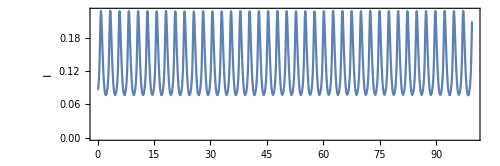

{2,10000,1000.}

```mathematica
mdata={};
file=OpenRead["data.txt"];
While[((line=ReadLine[file]) =!= EndOfFile),
AppendTo[mdata,Internal`StringToDouble/@StringSplit[line]];]
Close[file];
tdata=Transpose[mdata];
times=Range[Length[tdata[[1]]]]*1/200;
ListPlot[{Transpose[{times,tdata[[1]]}][[All]]},Joined->True,PlotRange->{All,All},AspectRatio->1/3,Frame->True,Axes->False,ImageSize->500,FrameLabel->{t,"I"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

{2,10000,1000.}

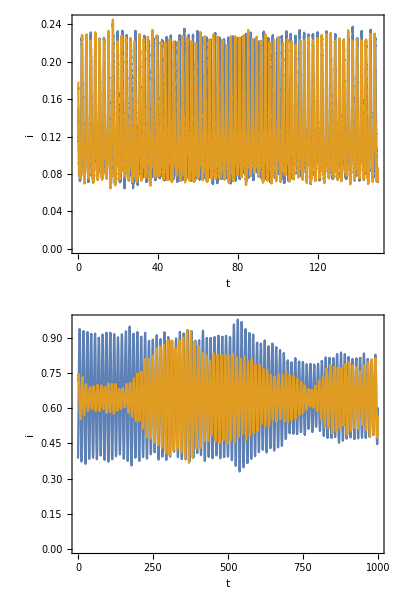

traces.pdf

```mathematica
file="data/uncorrelated/1";
strlst=ReadList[file<>".out",String];
{n,Nt,t1}=ToExpression[StringSplit[strlst[[3]]]][[1;;3]]
AbsoluteTiming[dat=Partition[Partition[BinaryReadList[file<>".dat","Real64"], 2],n]];
data=Transpose[dat[[1;;Length[dat]]],{2,1,3}];
e1=data[[1,All,1]];
theta1=data[[1,All,2]];
e2=data[[2,All,1]];
theta2=data[[2,All,2]];
Ch=1600;
a=0.3;
times=Range[Nt]/Nt*t1;
sig1=(Ch*Exp[0.5*e1]/(1+Ch*Exp[e1])+a*Exp[e1])*(1-theta1);
sig2=(Ch*Exp[0.5*e2]/(1+Ch*Exp[e2])+a*Exp[e2])*(1-theta2);

sigs1=Partition[Internal`StringToDouble/@DeleteCases[StringSplit[Import["data/experiments/exp1.txt"],{"   ","\n"}],""],7];
p=Grid[{{ListPlot[{Transpose[{Range[Length[sigs1]]*1/200,sigs1[[All,4]]}][[1;;30000]],Transpose[{Range[Length[sigs1]]*1/200,sigs1[[All,5]]}][[1;;30000]]},Joined->True,PlotRange->{All,All},AspectRatio->1/3,Frame->True,Axes->False,ImageSize->500,FrameLabel->{{"i",None},{t,"Experiments"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{55,15},{55,55}}]},{ListPlot[{Transpose[{times,sig1}][[1;;-1]],Transpose[{times,sig2}][[1;;-1]]},Joined->True,PlotRange->{All,All},AspectRatio->1/3,Frame->True,Axes->False,ImageSize->500,FrameLabel->{{"i",None},{t,"Simulations"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{55,15},{55,55}}]}}]
Export["traces.pdf",p]
```

#### Supplemental plots

```mathematica
sigs1=Partition[Internal`StringToDouble/@DeleteCases[StringSplit[Import["data/experiments/exp1.txt"],{"   ","\n"}],""],7];
times1=sigs1[[All,1]];
AbsoluteTiming[p1=getphase[sigs1[[All,2]]];]
AbsoluteTiming[p2=getphase[sigs1[[All,3]]];]
AbsoluteTiming[p3=getphase[sigs1[[All,4]]];]
AbsoluteTiming[p4=getphase[sigs1[[All,5]]];]
AbsoluteTiming[p5=getphase[sigs1[[All,6]]];]
AbsoluteTiming[p6=getphase[sigs1[[All,7]]];]
ediffs1=Mod[p1-p2+Pi,2*Pi]-Pi;
ediffs2=Mod[p3-p4+Pi,2*Pi]-Pi;
ediffs3=Mod[p5-p6+Pi,2*Pi]-Pi;
```

{12.1136,Null}

{11.9162,Null}

{11.766,Null}

{11.8172,Null}

{12.2178,Null}

{11.7321,Null}

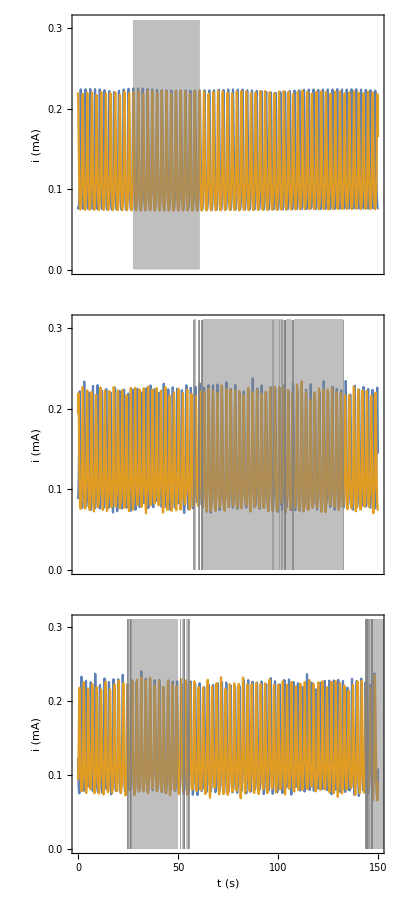

```mathematica
i1=10000;
i2=40000;
di=25;
thrs=Pi/4;
stimes1=Flatten[Position[ediffs1,u_/;Abs[u]<thrs]];
stimes1=stimes1[[Cases[Range[Length[stimes1]],u_Integer/;If[u==1,False,stimes1[[u]]-stimes1[[u-1]]==1] || If[u==Length[stimes1],False,stimes1[[u+1]]-stimes1[[u]]==1]]]];
atimes1=Flatten[Position[Differences[stimes1],u_/;u>1]];
synctimes1=(times1[[stimes1[[#]]]]-times1[[i1]])&/@Table[{atimes1[[i]]+1,atimes1[[i+1]]},{i,1,Length[atimes1]-1}];
stimes2=Flatten[Position[ediffs2,u_/;Abs[u]<thrs]];
stimes2=stimes2[[Cases[Range[Length[stimes2]],u_Integer/;If[u==1,False,stimes2[[u]]-stimes2[[u-1]]==1] || If[u==Length[stimes2],False,stimes2[[u+1]]-stimes2[[u]]==1]]]];
atimes2=Flatten[Position[Differences[stimes2],u_/;u>1]];
synctimes2=(times1[[stimes2[[#]]]]-times1[[i1]])&/@Table[{atimes2[[i]]+1,atimes2[[i+1]]},{i,1,Length[atimes2]-1}];
stimes3=Flatten[Position[ediffs3,u_/;Abs[u]<thrs]];
stimes3=stimes3[[Cases[Range[Length[stimes3]],u_Integer/;If[u==1,False,stimes3[[u]]-stimes3[[u-1]]==1] || If[u==Length[stimes3],False,stimes3[[u+1]]-stimes3[[u]]==1]]]];
atimes3=Flatten[Position[Differences[stimes3],u_/;u>1]];
synctimes3=(times1[[stimes3[[#]]]]-times1[[i1]])&/@Table[{atimes3[[i]]+1,atimes3[[i+1]]},{i,1,Length[atimes3]-1}];

plot1=Grid[{{ListPlot[{Transpose[{times1-times1[[i1]],sigs1[[All,2]]}][[i1;;i2;;di]],Transpose[{times1-times1[[i1]],sigs1[[All,3]]}][[i1;;i2;;di]]},Joined->True,PlotRange->{All,{0,0.31}},AspectRatio->1/5,Frame->True,Axes->False,ImageSize->600,FrameLabel->{{"i (mA)",None},{None,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{15,15}},Epilog->{Opacity[0.5],Gray,Rectangle[{#[[1]],0},{#[[2]],0.31}]&/@synctimes1},FrameTicks->{{Table[{i,PaddedForm[i,{1,1}]},{i,0,0.3,0.1}],Table[{i,""},{i,0,0.3,0.1}]},{Table[{i,""},{i,0,200,50}],Table[{i,""},{i,0,200,50}]}}]},{ListPlot[{Transpose[{times1-times1[[i1]],sigs1[[All,4]]}][[i1;;i2;;di]],Transpose[{times1-times1[[i1]],sigs1[[All,5]]}][[i1;;i2;;di]]},Joined->True,PlotRange->{All,{0,0.31}},AspectRatio->1/5,Frame->True,Axes->False,ImageSize->600,FrameLabel->{{"i (mA)",None},{None,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{15,15}},Epilog->{Opacity[0.5],Gray,Rectangle[{#[[1]],0},{#[[2]],0.31}]&/@synctimes2},FrameTicks->{{Table[{i,PaddedForm[i,{1,1}]},{i,0,0.3,0.1}],Table[{i,""},{i,0,0.3,0.1}]},{Table[{i,""},{i,0,200,50}],Table[{i,""},{i,0,200,50}]}}]},{ListPlot[{Transpose[{times1-times1[[i1]],sigs1[[All,6]]}][[i1;;i2;;di]],Transpose[{times1-times1[[i1]],sigs1[[All,7]]}][[i1;;i2;;di]]},Joined->True,PlotRange->{All,{0,0.31}},AspectRatio->1/5,Frame->True,Axes->False,ImageSize->600,FrameLabel->{{"i (mA)",None},{"t (s)",None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{55,15}},Epilog->{Opacity[0.5],Gray,Rectangle[{#[[1]],0},{#[[2]],0.31}]&/@synctimes3},FrameTicks->{{Table[{i,PaddedForm[i,{1,1}]},{i,0,0.3,0.1}],Table[{i,""},{i,0,0.3,0.1}]},{Table[{i,i},{i,0,200,50}],Table[{i,""},{i,0,200,50}]}}]}}]
```

```mathematica
diffs1={};
diffs2={};
diffs3={};
orders1={};
orders2={};
orders3={};
Monitor[Do[
AppendTo[orders1,ToExpression[StringSplit[ReadList["data/noiseless/"<>ToString[i]<>".out",String][[3]]]][[-1]]];
AppendTo[orders2,ToExpression[StringSplit[ReadList["data/correlated/"<>ToString[i]<>".out",String]][[3]]][[-1]]];AppendTo[orders3,ToExpression[StringSplit[ReadList["data/uncorrelated/"<>ToString[i]<>".out",String]][[3]]][[-1]]];
diffs1=Join[diffs1,Mod[-First@Differences[Partition[BinaryReadList["data/noiseless/"<>ToString[i]<>"phase.dat","Real64"],Length[BinaryReadList["data/noiseless/"<>ToString[i]<>"phase.dat","Real64"]]/2]]+Pi,2*Pi]-Pi];
diffs2=Join[diffs2,Mod[-First@Differences[Partition[BinaryReadList["data/correlated/"<>ToString[i]<>"phase.dat","Real64"],Length[BinaryReadList["data/correlated/"<>ToString[i]<>"phase.dat","Real64"]]/2]]+Pi,2*Pi]-Pi];
diffs3=Join[diffs3,Mod[-First@Differences[Partition[BinaryReadList["data/uncorrelated/"<>ToString[i]<>"phase.dat","Real64"],Length[BinaryReadList["data/uncorrelated/"<>ToString[i]<>"phase.dat","Real64"]]/2]]+Pi,2*Pi]-Pi];,{i,1,50}],i]
Mean/@{orders1,orders2,orders3}
```

{0.569178,0.574168,0.608744}

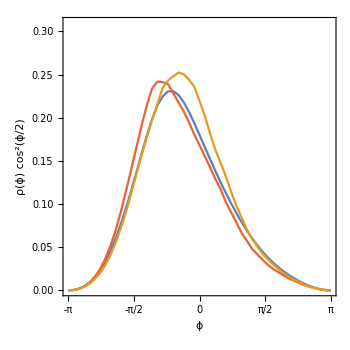

```mathematica
nbins=50;
plot2=ListPlot[{Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],Table[Cos[i/2]^2/(2*Pi/nbins),{i,-Pi,Pi,2*Pi/nbins}]*N[BinCounts[diffs1,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs1])]}],Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],Table[Cos[i/2]^2/(2*Pi/nbins),{i,-Pi,Pi,2*Pi/nbins}]*N[BinCounts[diffs2,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs2])]}],Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],Table[Cos[i/2]^2/(2*Pi/nbins),{i,-Pi,Pi,2*Pi/nbins}]*N[BinCounts[diffs3,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs3])]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{ϕ,Cos[DisplayForm[RowBox[{ϕ,"/",2}]]]^2*ρ[ϕ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[2]]]},ImageSize->350,PlotRange->{0,0.31},FrameTicks->{{{#,PaddedForm[#,{2,2}]}&/@#,{#,""}&/@#}&@Table[i,{i,0,0.3,0.05}],{{{-π,-π},{-π/2,DisplayForm[RowBox[{-Pi,"/",2}]]},{0,0},{π/2,DisplayForm[RowBox[{Pi,"/",2}]]},{π,π}},{{-π,""},{-π/2,""},{0,""},{π/2,""},{π,""}}}},AspectRatio->1]
```

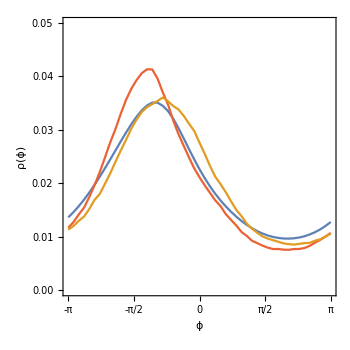

```mathematica
ListPlot[{Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],N[BinCounts[diffs1,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs1])]}],Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],N[BinCounts[diffs2,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs2])]}],Transpose[{Table[i,{i,-Pi,Pi,2*Pi/nbins}],N[BinCounts[diffs3,{-Pi,Pi,2*Pi/(nbins+1)}]/(Length[diffs3])]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{ϕ,ρ[ϕ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[2]]]},ImageSize->350,PlotRange->{0,0.05},FrameTicks->{{{#,PaddedForm[#,{2,2}]}&/@#,{#,""}&/@#}&@Table[i,{i,0,0.05,0.01}],{{{-π,-π},{-π/2,DisplayForm[RowBox[{-Pi,"/",2}]]},{0,0},{π/2,DisplayForm[RowBox[{Pi,"/",2}]]},{π,π}},{{-π,""},{-π/2,""},{0,""},{π/2,""},{π,""}}}},AspectRatio->1]
```

```mathematica
p=Grid[{{plot1,plot2}}]
Export["fig_electrodes.pdf",p]
```

-Graphics- | -Graphics-

fig_electrodes.pdf

#### Experimental time - series with protophase correction

```mathematica
sigs1=Partition[Internal`StringToDouble/@DeleteCases[StringSplit[Import["data/experiments/exp1.txt"],{"   ","\n"}],""],7];
sigs2=Partition[Internal`StringToDouble/@DeleteCases[StringSplit[Import["data/experiments/exp2.txt"],{"   ","\n"}],""],7];
times1=sigs1[[All,1]];
times2=sigs2[[All,1]];
AbsoluteTiming[p1=getphase[sigs1[[All,2]]];]
AbsoluteTiming[p2=getphase[sigs1[[All,3]]];]
AbsoluteTiming[p3=getphase[sigs1[[All,4]]];]
AbsoluteTiming[p4=getphase[sigs1[[All,5]]];]
AbsoluteTiming[p5=getphase[sigs1[[All,6]]];]
AbsoluteTiming[p6=getphase[sigs1[[All,7]]];]
AbsoluteTiming[p7=getphase[sigs2[[All,2]]];]
AbsoluteTiming[p8=getphase[sigs2[[All,3]]];]
AbsoluteTiming[p9=getphase[sigs2[[All,4]]];]
AbsoluteTiming[p10=getphase[sigs2[[All,5]]];]
AbsoluteTiming[p11=getphase[sigs2[[All,6]]];]
AbsoluteTiming[p12=getphase[sigs2[[All,7]]];]
```

{12.0581,Null}

{12.1299,Null}

{11.9239,Null}

{11.864,Null}

{12.0538,Null}

{12.8116,Null}

{12.6592,Null}

{13.7094,Null}

{13.089,Null}

{12.49,Null}

{12.2264,Null}

{16.9848,Null}

```mathematica
e1={Mean[(Abs[Exp[I*p1]+Exp[I*p2]])[[1;;-1;;1]]/2],Mean[(Abs[Exp[I*p3]+Exp[I*p4]])[[1;;-1;;1]]/2],Mean[(Abs[Exp[I*p5]+Exp[I*p6]])[[1;;-1;;1]]/2]}
Partition[Internal`StringToDouble/@DeleteCases[Flatten[StringSplit[StringSplit[Import["D005-Values.txt"],"   "],"\n"]],""],3][[All,{3,1,2}]]
e2={Mean[(Abs[Exp[I*p7]+Exp[I*p8]])[[1;;-1;;1]]/2],Mean[(Abs[Exp[I*p9]+Exp[I*p10]])[[1;;-1;;1]]/2],Mean[(Abs[Exp[I*p11]+Exp[I*p12]])[[1;;-1;;1]]/2]}
Partition[Internal`StringToDouble/@DeleteCases[Flatten[StringSplit[StringSplit[Import["D010-Values.txt"],"   "],"\n"]],""],3][[All,{3,1,2}]]

Norm[#-e1]&/@Partition[Internal`StringToDouble/@DeleteCases[Flatten[StringSplit[StringSplit[Import["D005-Values.txt"],"   "],"\n"]],""],3][[All,{3,1,2}]]
Norm[#-e2]&/@Partition[Internal`StringToDouble/@DeleteCases[Flatten[StringSplit[StringSplit[Import["D010-Values.txt"],"   "],"\n"]],""],3][[All,{3,1,2}]]
```

{0.619527,0.717896,0.679589}

{{0.643742,0.721713,0.685993},{0.618359,0.646524,0.564352},{0.632418,0.700481,0.66032},{0.593581,0.645647,0.661322},{0.607071,0.645226,0.605038},{0.66814,0.726459,0.60913},{0.649191,0.656505,0.7157},{0.614141,0.721668,0.688464},{0.679637,0.71368,0.736435},{0.648409,0.743281,0.607031},{0.62292,0.738975,0.731065},{0.644341,0.731486,0.743498},{0.675755,0.664298,0.633746},{0.6482,0.741131,0.645144},{0.61882,0.678179,0.612392},{0.671894,0.704384,0.6827},{0.677698,0.676161,0.688624},{0.689,0.673872,0.665553},{0.678711,0.666373,0.689235},{0.62184,0.712035,0.707662},{0.566653,0.637992,0.638085},{0.610183,0.685317,0.681016}}

{0.66324,0.804769,0.695606}

{{0.629076,0.648321,0.792814},{0.64965,0.746627,0.796973},{0.658997,0.802638,0.699984},{0.71482,0.767146,0.870105},{0.68566,0.751469,0.871935},{0.625666,0.632834,0.728244},{0.63311,0.638422,0.840154},{0.641798,0.692549,0.877062},{0.706332,0.673064,0.795001},{0.576771,0.756825,0.798901}}

{0.0253362,0.135554,0.0289964,0.0789112,0.104853,0.0860293,0.0771546,0.0110451,0.0828393,0.0821173,0.0557276,0.0698907,0.0901993,0.0504825,0.0780612,0.0541712,0.0721615,0.0834361,0.0790594,0.0287715,0.104417,0.0339232}

{0.18733,0.117646,0.0064586,0.185812,0.185568,0.178994,0.222426,0.214429,0.170537,0.142988}

```mathematica
{Mean[((Abs[Exp[I*p1]+Exp[I*p2]])[[100;;-100;;1]]/2)^2],Mean[((Abs[Exp[I*p3]+Exp[I*p4]])[[100;;-100;;1]]/2)^2],Mean[((Abs[Exp[I*p5]+Exp[I*p6]])[[100;;-100;;1]]/2)^2]}
{Mean[((Abs[Exp[I*p7]+Exp[I*p8]])[[100;;-100;;1]]/2)^2],Mean[((Abs[Exp[I*p9]+Exp[I*p10]])[[100;;-100;;1]]/2)^2],Mean[((Abs[Exp[I*p11]+Exp[I*p12]])[[100;;-100;;1]]/2)^2]}
```

{0.471832,0.592231,0.549382}

{0.517529,0.701005,0.569817}

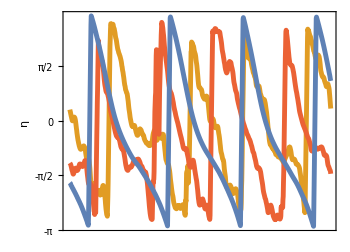
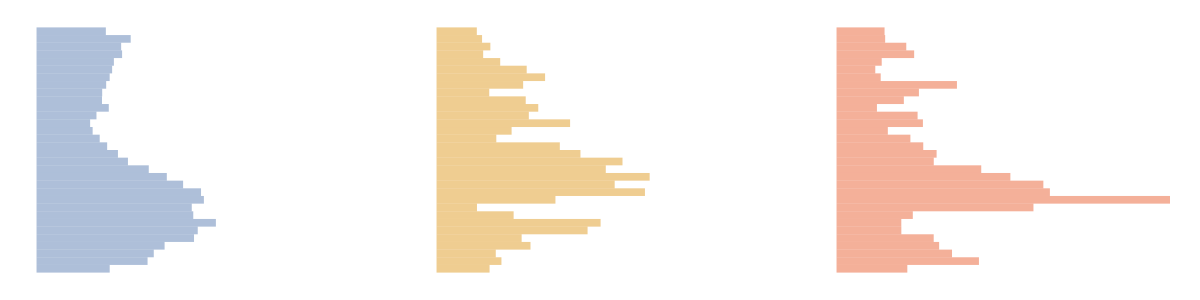
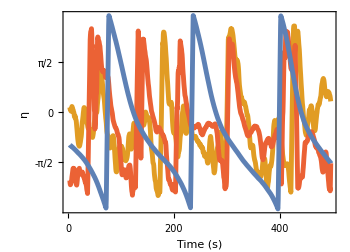
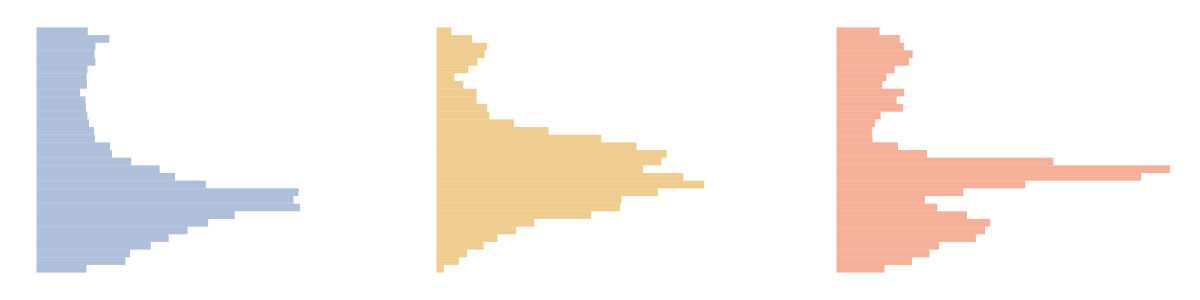
-Graphics- | -Graphics-
-Graphics- | -Graphics-

experiments_histograms.pdf

```mathematica
p=Grid[{{ListPlot[{MovingAverage[Transpose[{times1,Mod[p3-p4+Pi,2*Pi]-Pi}],1000],MovingAverage[Transpose[{times1,Mod[p5-p6+Pi,2*Pi]-Pi}],1000],MovingAverage[Transpose[{times1,Mod[p1-p2+Pi,2*Pi]-Pi}],1000]}[[All,100;;-100;;100]],Joined->True,Frame->True,FrameLabel->{None,η},FrameStyle->Directive[AbsoluteThickness[1],Black],LabelStyle->Directive[16,Black], PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[4]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]]},ImageSize->{350,225},AspectRatio->(225-5-10)/(350-55-5),ImagePadding->{{55,10},{5,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,-Pi,Pi,Pi/2}],Table[{i,""},{i,-Pi,Pi,Pi/2}]},{Table[{i,""},{i,0,500,100}],Table[{i,""},{i,0,500,100}]}}],Grid[{{Histogram[{Mod[p1-p2+Pi,2*Pi]-Pi},25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],ColorData[97,"ColorList"][[1]]]},BarOrigin->Left,Axes->False,ImageSize->{100,225},AspectRatio->3,ImagePadding->{{5,10},{5,10}}],Histogram[{Mod[p3-p4+Pi,2*Pi]-Pi},25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],ColorData[97,"ColorList"][[2]]],Directive[EdgeForm[],ColorData[97,"ColorList"][[4]]],Directive[EdgeForm[],ColorData[97,"ColorList"][[1]]]},BarOrigin->Left,Axes->False,ImageSize->{100,225},AspectRatio->3,ImagePadding->{{5,10},{5,10}}],
Histogram[{Mod[p5-p6+Pi,2*Pi]-Pi},25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],ColorData[97,"ColorList"][[4]]]},BarOrigin->Left,Axes->False,ImageSize->{100,225},AspectRatio->3,ImagePadding->{{5,10},{5,10}}]}}]},{ListPlot[{MovingAverage[Transpose[{times1,Mod[p9-p10+Pi,2*Pi]-Pi}],1000],MovingAverage[Transpose[{times1,Mod[p11-p12+Pi,2*Pi]-Pi}],1000],MovingAverage[Transpose[{times1,Mod[p7-p8+Pi,2*Pi]-Pi}],1000]}[[All,100;;-100;;100]],Joined->True,Frame->True,FrameLabel->{"Time (s)",η},FrameStyle->Directive[AbsoluteThickness[1],Black],LabelStyle->Directive[16,Black], PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[4]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]]},ImageSize->{350,275},AspectRatio->(275-55-10)/(350-55-5),ImagePadding->{{55,10},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,-Pi,Pi,Pi/2}],Table[{i,""},{i,-Pi,Pi,Pi/2}]},{Table[i,{i,0,500,100}],Table[{i,""},{i,0,500,100}]}}],Grid[{{Histogram[{Mod[p7-p8+Pi,2*Pi]-Pi},25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],ColorData[97,"ColorList"][[1]]]},BarOrigin->Left,Axes->False,ImageSize->{100,275},AspectRatio->3,ImagePadding->{{5,10},{55,5}}],Histogram[{Mod[p9-p10+Pi,2*Pi]-Pi},25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],ColorData[97,"ColorList"][[2]]],Directive[EdgeForm[],ColorData[97,"ColorList"][[4]]],Directive[EdgeForm[],ColorData[97,"ColorList"][[1]]]},BarOrigin->Left,Axes->False,ImageSize->{100,275},AspectRatio->3,ImagePadding->{{5,10},{55,5}}],
Histogram[{Mod[p11-p12+Pi,2*Pi]-Pi},25,"Probability",PlotRange->{0,1/10},ChartStyle->{Directive[EdgeForm[],ColorData[97,"ColorList"][[4]]]},BarOrigin->Left,Axes->False,ImageSize->{100,275},AspectRatio->3,ImagePadding->{{5,10},{55,5}}]}}]}}]
Export["experiments_histograms.pdf",p]
```

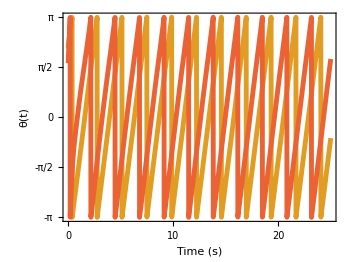

```mathematica
ListPlot[{Transpose[{times1,Mod[p1+Pi,2*Pi]-Pi}],Transpose[{times1,Mod[p2+Pi,2*Pi]-Pi}]}[[All,1;;5000;;1]],Joined->True,Frame->True,FrameLabel->{"Time (s)",θ[t]},FrameStyle->Directive[AbsoluteThickness[1],Black],LabelStyle->Directive[16,Black], PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[4]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]]},ImageSize->350,AspectRatio->0.75,ImagePadding->{{55,10},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,-Pi,Pi,Pi/2}],Table[{i,""},{i,-Pi,Pi,Pi/2}]},{Table[i,{i,0,25,5}],Table[{i,""},{i,0,25,5}]}}]
```

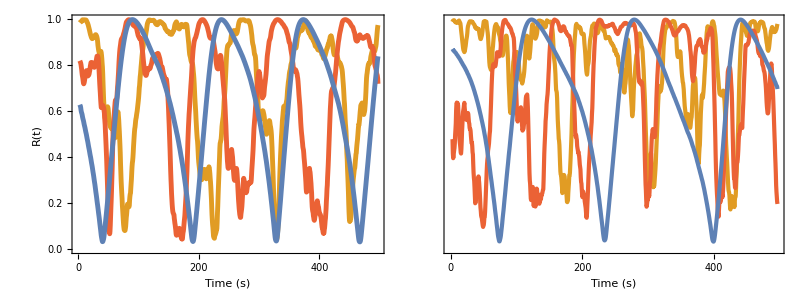

experiments.pdf

```mathematica
p=Grid[{{ListPlot[{MovingAverage[Transpose[{times1,Abs[Exp[I*p3]+Exp[I*p4]]/2}],1000],MovingAverage[Transpose[{times1,Abs[Exp[I*p5]+Exp[I*p6]]/2}],1000],MovingAverage[Transpose[{times1,Abs[Exp[I*p1]+Exp[I*p2]]/2}],1000]}[[All,100;;-100;;100]],Joined->True,Frame->True,FrameLabel->{"Time (s)",R[t]},FrameStyle->Directive[AbsoluteThickness[1],Black],LabelStyle->Directive[16,Black], PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[4]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]]},ImageSize->350,AspectRatio->0.75,ImagePadding->{{55,10},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]},{Table[i,{i,0,500,100}],Table[{i,""},{i,0,500,100}]}}],ListPlot[{MovingAverage[Transpose[{times1,Abs[Exp[I*p9]+Exp[I*p10]]/2}],1000],MovingAverage[Transpose[{times1,Abs[Exp[I*p11]+Exp[I*p12]]/2}],1000],MovingAverage[Transpose[{times1,Abs[Exp[I*p7]+Exp[I*p8]]/2}],1000]}[[All,100;;-100;;100]],Joined->True,Frame->True,FrameLabel->{"Time (s)",None},FrameStyle->Directive[AbsoluteThickness[1],Black],LabelStyle->Directive[16,Black], PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[4]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]]},ImageSize->300,AspectRatio->0.75,ImagePadding->{{5,10},{55,5}},FrameTicks->{{Table[{i,""},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]},{Table[i,{i,0,500,100}],Table[{i,""},{i,0,500,100}]}}]}},Spacings->0]
Export["experiments.pdf",p]
```

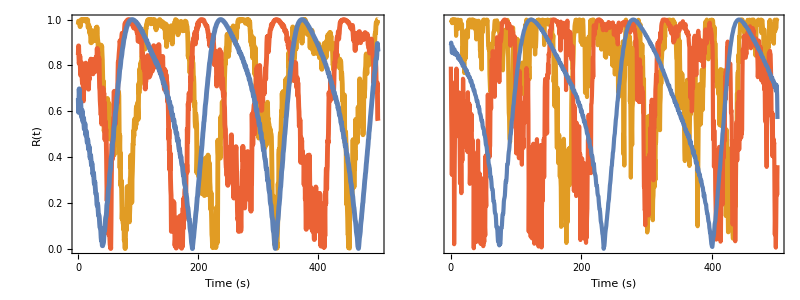

```mathematica
Grid[{{ListPlot[{Transpose[{times1,Abs[Exp[I*p3]+Exp[I*p4]]/2}],Transpose[{times1,Abs[Exp[I*p5]+Exp[I*p6]]/2}],Transpose[{times1,Abs[Exp[I*p1]+Exp[I*p2]]/2}]}[[All,100;;-100;;100]],Joined->True,Frame->True,FrameLabel->{"Time (s)",R[t]},FrameStyle->Directive[AbsoluteThickness[1],Black],LabelStyle->Directive[16,Black], PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[4]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]]},ImageSize->350,AspectRatio->0.75,ImagePadding->{{55,10},{55,5}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]},{Table[i,{i,0,500,100}],Table[{i,""},{i,0,500,100}]}}],ListPlot[{Transpose[{times1,Abs[Exp[I*p9]+Exp[I*p10]]/2}],Transpose[{times1,Abs[Exp[I*p11]+Exp[I*p12]]/2}],Transpose[{times1,Abs[Exp[I*p7]+Exp[I*p8]]/2}]}[[All,100;;-100;;100]],Joined->True,Frame->True,FrameLabel->{"Time (s)",None},FrameStyle->Directive[AbsoluteThickness[1],Black],LabelStyle->Directive[16,Black], PlotStyle->{Directive[Thickness[0.01],ColorData[97,"ColorList"][[2]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[4]]],Directive[Thickness[0.01],ColorData[97,"ColorList"][[1]]]},ImageSize->300,AspectRatio->0.75,ImagePadding->{{5,10},{55,5}},FrameTicks->{{Table[{i,""},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]},{Table[i,{i,0,500,100}],Table[{i,""},{i,0,500,100}]}}]}},Spacings->0]
```

```mathematica
d005=Internal`StringToDouble/@DeleteCases[Flatten[StringSplit[StringSplit[Import["D005-Values.txt"],"   "],"\n"]],""];
d010=Internal`StringToDouble/@DeleteCases[Flatten[StringSplit[StringSplit[Import["D010-Values.txt"],"   "],"\n"]],""];
d025=Internal`StringToDouble/@DeleteCases[Flatten[StringSplit[StringSplit[Import["D0025-Values.txt"],"   "],"\n"]],""];
```

PairedTTest::nortst: At least one of the p-values in {0.00113398,0.553186}, resulting from a test for normality, is below 0.025. The tests in {PairedT} require that the data is normally distributed.

PairedTTest::nortst: At least one of the p-values in {0.37012,0.00113398}, resulting from a test for normality, is below 0.025. The tests in {PairedT} require that the data is normally distributed.

{0.693797,0.0989884,0.62137}

{0.999994,0.979099,0.976797}

{0.980443,0.993614,0.999968}

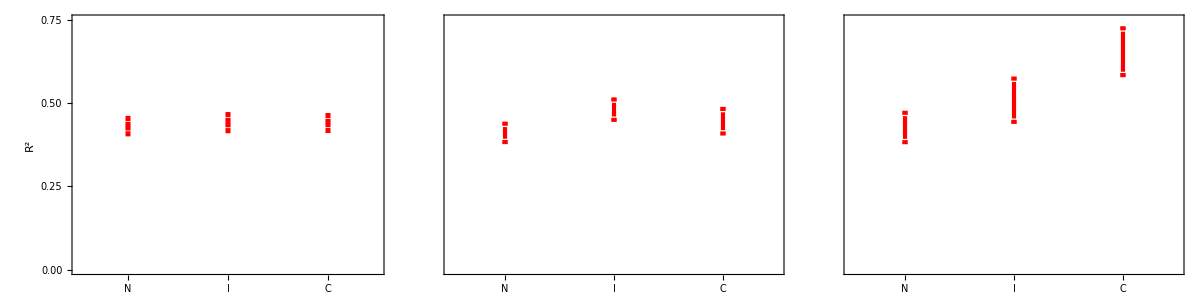

```mathematica
small=(Transpose[Partition[d025,3]]^2)[[{3,1,2}]];
moderate=(Transpose[Partition[d005,3]]^2)[[{3,1,2}]];
large=(Transpose[Partition[d010,3]]^2)[[{3,1,2}]];
1-{PairedTTest[small[[{1,2},All]]],PairedTTest[small[[{2,3},All]]],PairedTTest[small[[{3,1},All]]]}
1-{PairedTTest[moderate[[{1,2},All]]],PairedTTest[moderate[[{2,3},All]]],PairedTTest[moderate[[{3,1},All]]]}
1-{PairedTTest[large[[{1,2},All]]],PairedTTest[large[[{2,3},All]]],PairedTTest[large[[{3,1},All]]]}

errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Red,Thickness[0.01],Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{(x0+x1)/2+1/16*(x1-x0),y1+error+0.01},{(x0+x1)/2-1/16*(x1-x0),y1+error+0.01}},{{(x0+x1)/2+1/16*(x1-x0),y1-error-0.01},{(x0+x1)/2-1/16*(x1-x0),y1-error-0.01}}}]}}]
labels={"N","I","C"};
p1=BarChart[Mean[#]-> 2*StandardDeviation[#]/Length[#]^(1/2)&/@small,ChartElementFunction->errorBar["Rectangle"],Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],BarSpacing->1.5,ChartStyle->Directive[White,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.75,0.25}],Table[{i,""},{i,0,0.75,0.25}]},{Table[{i,labels[[i]]},{i,1,3}],Table[{i,""},{i,1,3}]}},PlotRange->{{0.5,3.5},{0,0.75}},AspectRatio->0.75,ImageSize->370,ImagePadding->{{75,10},{25,35}},FrameLabel->{{R^2,None},{None,D==0.025V}},LabelStyle->Directive[18,Black]];
p2=BarChart[Mean[#]-> 2*StandardDeviation[#]/Length[#]^(1/2)&/@moderate,ChartElementFunction->errorBar["Rectangle"],Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],BarSpacing->1.5,ChartStyle->Directive[White,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]],FrameTicks->{{Table[{i,""},{i,0,0.75,0.25}],Table[{i,""},{i,0,0.75,0.25}]},{Table[{i,labels[[i]]},{i,1,3}],Table[{i,""},{i,1,3}]}},PlotRange->{{0.5,3.5},{0,0.75}},AspectRatio->0.75,ImageSize->300,ImagePadding->{{5,10},{25,35}},FrameLabel->{{None,None},{None,D==0.05V}},LabelStyle->Directive[18,Black]];
p3=BarChart[Mean[#]-> 2*StandardDeviation[#]/Length[#]^(1/2)&/@large,ChartElementFunction->errorBar["Rectangle"],Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],BarSpacing->1.5,ChartStyle->Directive[White,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]],FrameTicks->{{Table[{i,""},{i,0,0.75,0.25}],Table[{i,""},{i,0,0.75,0.25}]},{Table[{i,labels[[i]]},{i,1,3}],Table[{i,""},{i,1,3}]}},PlotRange->{{0.5,3.5},{0,0.75}},AspectRatio->0.75,ImageSize->300,ImagePadding->{{5,10},{25,35}},FrameLabel->{{None,None},{None,D==PaddedForm[0.10,{2,2}]V}},LabelStyle->Directive[18,Black]];
p=Grid[{{p1,p2,p3}},Spacings->0]
```

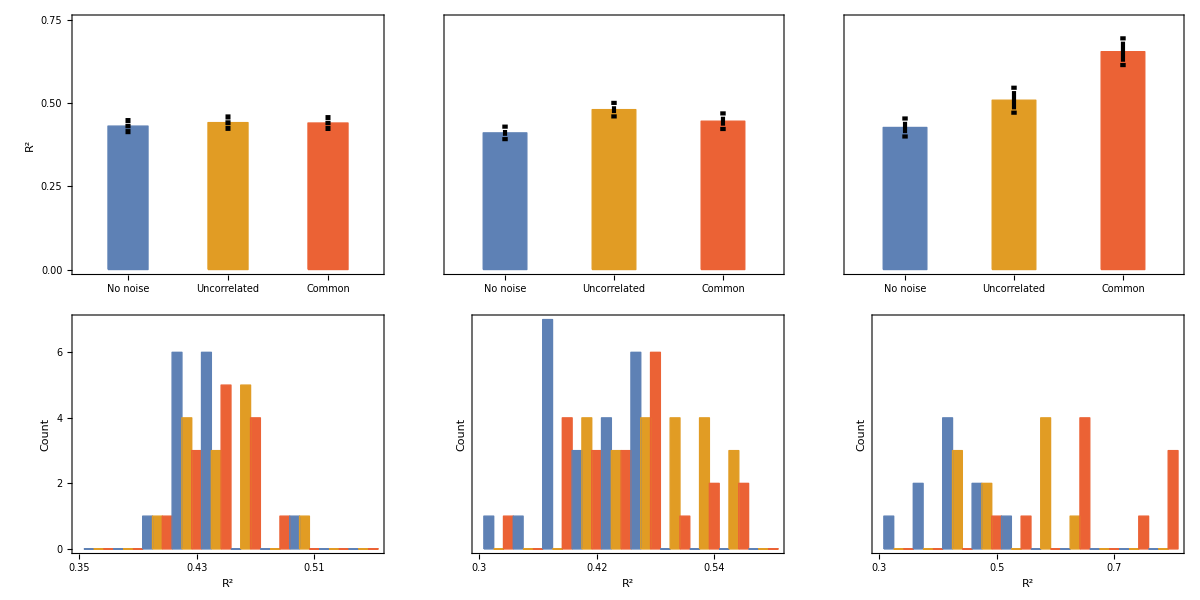

bars.pdf

```mathematica
errorBar[type_: "Rectangle"][{{x0_,x1_},{y0_,y1_}},value_,meta_]:=Block[{error,mags=QuantityMagnitude[value]},error=Flatten[QuantityMagnitude[meta]];
error=If[error==={},0,Last[error]];{ChartElementData[type][{{x0,x1},{y0,y1}},mags,meta],{Black,Thickness[0.01],Line[{{{(x0+x1)/2,y1-error},{(x0+x1)/2,y1+error}},{{(x0+x1)/2+1/16*(x1-x0),y1+error+0.01},{(x0+x1)/2-1/16*(x1-x0),y1+error+0.01}},{{(x0+x1)/2+1/16*(x1-x0),y1-error-0.01},{(x0+x1)/2-1/16*(x1-x0),y1-error-0.01}}}]}}]
labels={Rotate["No noise",-Pi/3],Rotate["Uncorrelated",-Pi/3],Rotate["Common",-Pi/3]};
p1=BarChart[Mean[#]-> StandardDeviation[#]/Length[#]^(1/2)&/@small,ChartElementFunction->errorBar["Rectangle"],Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],BarSpacing->1.5,ChartStyle->(Directive[#,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]]&/@ColorData[97,"ColorList"][[{1,2,4}]]),FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.75,0.25}],Table[{i,""},{i,0,0.75,0.25}]},{Table[{i,labels[[i]]},{i,1,3}],Table[{i,""},{i,1,3}]}},PlotRange->{{0.5,3.5},{0,0.75}},AspectRatio->0.75,ImageSize->370,ImagePadding->{{75,10},{25,35}},FrameLabel->{{R^2,None},{None,D==0.025V}},LabelStyle->Directive[18,Black]];
p2=BarChart[Mean[#]-> StandardDeviation[#]/Length[#]^(1/2)&/@moderate,ChartElementFunction->errorBar["Rectangle"],Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],BarSpacing->1.5,ChartStyle->(Directive[#,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]]&/@ColorData[97,"ColorList"][[{1,2,4}]]),FrameTicks->{{Table[{i,""},{i,0,0.75,0.25}],Table[{i,""},{i,0,0.75,0.25}]},{Table[{i,labels[[i]]},{i,1,3}],Table[{i,""},{i,1,3}]}},PlotRange->{{0.5,3.5},{0,0.75}},AspectRatio->0.75,ImageSize->300,ImagePadding->{{5,10},{25,35}},FrameLabel->{{None,None},{None,D==0.05V}},LabelStyle->Directive[18,Black]];
p3=BarChart[Mean[#]-> StandardDeviation[#]/Length[#]^(1/2)&/@large,ChartElementFunction->errorBar["Rectangle"],Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],BarSpacing->1.5,ChartStyle->(Directive[#,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]]&/@ColorData[97,"ColorList"][[{1,2,4}]]),FrameTicks->{{Table[{i,""},{i,0,0.75,0.25}],Table[{i,""},{i,0,0.75,0.25}]},{Table[{i,labels[[i]]},{i,1,3}],Table[{i,""},{i,1,3}]}},PlotRange->{{0.5,3.5},{0,0.75}},AspectRatio->0.75,ImageSize->300,ImagePadding->{{5,10},{25,35}},FrameLabel->{{None,None},{None,D==PaddedForm[0.10,{2,2}]V}},LabelStyle->Directive[18,Black]];
p4=BarChart[Transpose[BinCounts[#,{0.35,0.55,0.02}]&/@small],Axes->False,Frame->True,FrameLabel->{{Count,None},{R^2,None}},LabelStyle->Directive[18,Black],ChartStyle->(Directive[#,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]]&/@ColorData[97,"ColorList"][[{1,2,4}]]),FrameStyle->Directive[AbsoluteThickness[1.5],Black],AspectRatio->0.25,BarSpacing->0,FrameTicks->{{Table[i,{i,0,7,2}],Table[{i,""},{i,0,7,2}]},{Table[{6*(i-0.35)/0.04,i},{i,0.35,0.55,0.04}],Table[{6*(i-0.35)/0.04,""},{i,0.35,0.55,0.04}]}},ImageSize->370,PlotRange->{0,7},ImagePadding->{{75,10},{55,5}}];
p5=BarChart[Transpose[BinCounts[#,{0.3,0.6,0.03}]&/@moderate],Axes->False,Frame->True,FrameLabel->{{Count,None},{R^2,None}},LabelStyle->Directive[18,Black],ChartStyle->(Directive[#,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]]&/@ColorData[97,"ColorList"][[{1,2,4}]]),FrameStyle->Directive[AbsoluteThickness[1.5],Black],AspectRatio->0.25,BarSpacing->0,FrameTicks->{{Table[{i,""},{i,0,7,2}],Table[{i,""},{i,0,7,2}]},{Table[{6*(i-0.3)/0.06,i},{i,0.3,0.6,0.06}],Table[{6*(i-0.3)/0.06,""},{i,0.3,0.6,0.06}]}},ImageSize->300,PlotRange->{0,7},ImagePadding->{{5,10},{55,5}}];
p6=BarChart[Transpose[BinCounts[#,{0.3,0.8,0.05}]&/@large],Axes->False,Frame->True,FrameLabel->{{Count,None},{R^2,None}},LabelStyle->Directive[18,Black],ChartStyle->(Directive[#,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]]&/@ColorData[97,"ColorList"][[{1,2,4}]]),FrameStyle->Directive[AbsoluteThickness[1.5],Black],AspectRatio->0.25,BarSpacing->0,FrameTicks->{{Table[{i,""},{i,0,7,2}],Table[{i,""},{i,1,7,2}]},{Table[{6*(i-0.3)/0.1,i},{i,0.3,0.8,0.1}],Table[{6*(i-0.3)/0.1,""},{i,0.3,0.75,0.1}]}},ImageSize->300,PlotRange->{0,7},ImagePadding->{{5,10},{55,5}}];
p=Grid[{{p1,p2,p3},{p4,p5,p6}},Spacings->0]
Export["bars.pdf",p]
```

{No noise,Uncorrelated,Common}

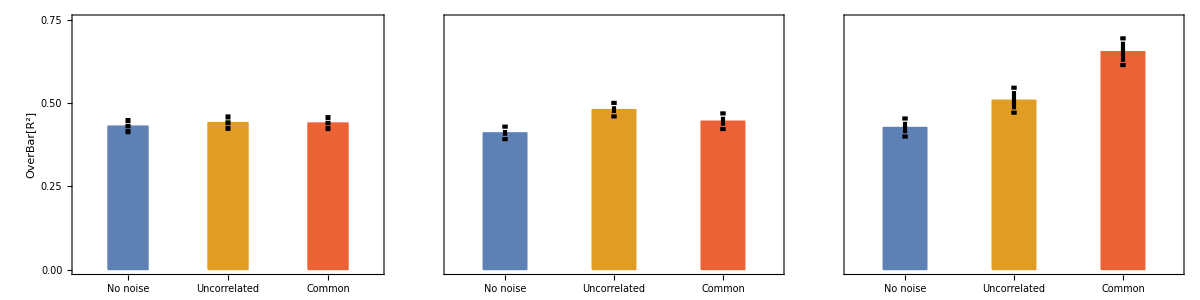

bars.pdf

```mathematica
labels={Rotate["No noise",-Pi/4],Rotate["Uncorrelated",-Pi/4],Rotate["Common",-Pi/4]}
p1=BarChart[Mean[#]-> StandardDeviation[#]/Length[#]^(1/2)&/@small,ChartElementFunction->errorBar["Rectangle"],Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],BarSpacing->1.5,ChartStyle->(Directive[#,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]]&/@ColorData[97,"ColorList"][[{1,2,4}]]),FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.75,0.25}],Table[{i,""},{i,0,0.75,0.25}]},{Table[{i,labels[[i]]},{i,1,3}],Table[{i,""},{i,1,3}]}},PlotRange->{{0.5,3.5},{0,0.75}},AspectRatio->0.75,ImageSize->370,ImagePadding->{{75,10},{100,35}},FrameLabel->{{OverBar[R^2],None},{None,D==0.025V}},LabelStyle->Directive[18,Black]];
p2=BarChart[Mean[#]-> StandardDeviation[#]/Length[#]^(1/2)&/@moderate,ChartElementFunction->errorBar["Rectangle"],Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],BarSpacing->1.5,ChartStyle->(Directive[#,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]]&/@ColorData[97,"ColorList"][[{1,2,4}]]),FrameTicks->{{Table[{i,""},{i,0,0.75,0.25}],Table[{i,""},{i,0,0.75,0.25}]},{Table[{i,labels[[i]]},{i,1,3}],Table[{i,""},{i,1,3}]}},PlotRange->{{0.5,3.5},{0,0.75}},AspectRatio->0.75,ImageSize->300,ImagePadding->{{5,10},{100,35}},FrameLabel->{{None,None},{None,D==0.05V}},LabelStyle->Directive[18,Black]];
p3=BarChart[Mean[#]-> StandardDeviation[#]/Length[#]^(1/2)&/@large,ChartElementFunction->errorBar["Rectangle"],Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],BarSpacing->1.5,ChartStyle->(Directive[#,EdgeForm[Opacity[1]],EdgeForm[AbsoluteThickness[1]]]&/@ColorData[97,"ColorList"][[{1,2,4}]]),FrameTicks->{{Table[{i,""},{i,0,0.75,0.25}],Table[{i,""},{i,0,0.75,0.25}]},{Table[{i,labels[[i]]},{i,1,3}],Table[{i,""},{i,1,3}]}},PlotRange->{{0.5,3.5},{0,0.75}},AspectRatio->0.75,ImageSize->300,ImagePadding->{{5,10},{100,35}},FrameLabel->{{None,None},{None,D==PaddedForm[0.10,{2,2}]V}},LabelStyle->Directive[18,Black]];
p=Grid[{{p1,p2,p3}}]
Export["bars.pdf",p]
```